```mathematica
w
```

Part 0: Filtering the diagram

## Process a single image

```mathematica
trusses=Import["http://swscorp.net/wp-content/uploads/2014/08/trussestop.jpg"]
```

-Graphics-

```mathematica
diagram=ImageCrop[ImageCrop[trusses,{500,130},{Right,Top}],{500,115},Bottom]
```

-Graphics-

```mathematica
binaryDiagram=Dilation[ColorNegate[Binarize[ImageEffect[diagram,{"Posterization",2}]]],2]
```

-Graphics-

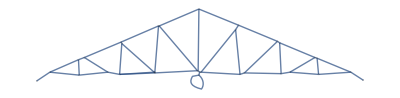

```mathematica
originalGraph=MorphologicalGraph[binaryDiagram]
```

```mathematica
originalGraph
```

## Normalize the image

## Process a whole image

## Code

### Tests:

### 1

### 2

### 3

### 4

### 5

Part I: Solving External Forces

## Input Ingredients

```mathematica
Clear[a,b,c,d,e]
```

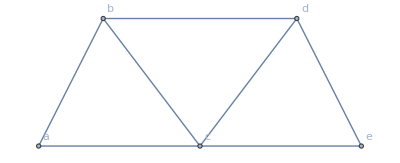

```mathematica
graph=Graph[{a<-> b, b <-> d, d <-> e, a <-> c, c <-> e, c <-> b, c <-> d}, VertexLabels -> Automatic,VertexCoordinates->{{0,0},{2,4},{8,4},{10,0},{5,0}}]
```

```mathematica
vertexList=graph//VertexList
```

{a,b,d,e,c}

```mathematica
vertexCoordinate= PropertyValue[graph,VertexCoordinates]
```

{{0,0},{2,4},{8,4},{10,0},{5,0}}

#### Input Forces: Support and Applied

```mathematica
appliedForces= {{b,{FS1,3*Pi/2}},{c,{FS2,3*Pi/2}},{d,{FS3,3*Pi/2}}}(*Force={Vertex, Force, Angle}*)
```

{{b,{FS1,(3 π)/2}},{c,{FS2,(3 π)/2}},{d,{FS3,(3 π)/2}}}

```mathematica
supportForces={{a,{S1,Pi/2}},{e,{S2,Pi/2}}}(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
```

{{a,{S1,π/2}},{e,{S2,π/2}}}

```mathematica
parallelSuppor={{a,{Sp,0}}}(*Parallel to the base support queue*)
```

{{a,{Sp,0}}}

## List of x and y components of external forces as well as x and y components of support forces

```mathematica
yComponent[magnitud_,angle_]:=magnitud*Sin[angle]
```

```mathematica
xComponent[magnitud_,angle_]:=magnitud*Cos[angle]
```

```mathematica
yApplied=Map[ yComponent[First[Last[#]],Last[Last[#]]]&,appliedForces,1](*The order of this list should be the same as applied projection*)
```

{-FS1,-FS2,-FS3}

```mathematica
xApplied=Map[ xComponent[First[Last[#]],Last[Last[#]]]&,appliedForces,1]
```

{0,0,0}

```mathematica
{0,0,0}
```

{0,0,0}

```mathematica
ySupport=Map[yComponent[First[Last[#]],Last[Last[#]]]&,supportForces,1]
```

{S1,S2}

```mathematica
xSupport=Map[yComponent[First[Last[#]],Last[Last[#]]]&,parallelSuppor,1]
```

{0}

## List of distance in the x direction of the vertices

```mathematica
appliedProjection=Extract[vertexCoordinate,#][[1]]&/@Map[Position[vertexList,First[#]][[1,1]]&,appliedForces]
```

{2,5,8}

```mathematica
supportProjection = Extract[vertexCoordinate,#][[1]]&/@Map[Position[vertexList,First[#]][[1,1]]&,supportForces]
```

{0,10}

## List of distance in the x direction with different origins

```mathematica
appliedProjection=Map[appliedProjection-supportProjection[[#]]&,Range[Length[supportProjection]]]
```

{{2,5,8},{-8,-5,-2}}

```mathematica
supportProjection =Map[supportProjection-supportProjection[[#]]&,Range[Length[supportProjection]]]
```

{{0,10},{-10,0}}

## List of moment equation for each coordinate system

```mathematica
applied=Dot[yApplied,#]&/@appliedProjection
```

{-2 FS1-5 FS2-8 FS3,8 FS1+5 FS2+2 FS3}

```mathematica
support=Dot[ySupport,#]&/@supportProjection
```

{10 S2,-10 S1}

```mathematica
externalTotal=applied+support
```

{-2 FS1-5 FS2-8 FS3+10 S2,8 FS1+5 FS2+2 FS3-10 S1}

```mathematica
externalEquations=Map[#== 0&,externalTotal]
```

{-2 FS1-5 FS2-8 FS3+10 S2==0,8 FS1+5 FS2+2 FS3-10 S1==0}

## Solve for all the support forces

```mathematica
externalSol=Solve[externalEquations,ySupport]
```

{{S1→1/10 (8 FS1+5 FS2+2 FS3),S2→1/10 (2 FS1+5 FS2+8 FS3)}}

```mathematica
AppendTo[externalSol,Sp-> -Total[xApplied]]
```

{{S1→1/10 (8 FS1+5 FS2+2 FS3),S2→1/10 (2 FS1+5 FS2+8 FS3)},Sp→0}

## Code

### Tests:

### 1

### 2

### 3

### 4

### 5

Part II: Solving Internal Forces

## Input Ingredients

```mathematica
Clear[a,b,c,d,e,Sp]
```

```mathematica
graph=Graph[{a<-> b, b <-> d, d <-> e, a <-> c, c <-> e, c <-> b, c <-> d}, VertexLabels -> Automatic,VertexCoordinates->{{0,0},{2,4},{8,4},{10,0},{5,0}}]
```

-Graphics-

```mathematica
vertexList=graph//VertexList
```

{a,b,d,e,c}

```mathematica
vertexCoordinate= PropertyValue[graph,VertexCoordinates]
```

{{0,0},{2,4},{8,4},{10,0},{5,0}}

```mathematica
vertexCoordinate= PropertyValue[graph,VertexCoordinates]
```

{{0,0},{2,4},{8,4},{10,0},{5,0}}

### Input Forces: Support and Applied

```mathematica
appliedForces= {{b,{FS1,3*Pi/2}},{c,{FS2,3*Pi/2}},{d,{FS3,3*Pi/2}}}(*Force={Vertex, Force, Angle}*)
```

{{b,{FS1,(3 π)/2}},{c,{FS2,(3 π)/2}},{d,{FS3,(3 π)/2}}}

```mathematica
supportForces={{a,{S1,Pi/2}},{e,{S2,Pi/2}}}(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
```

{{a,{S1,π/2}},{e,{S2,π/2}}}

```mathematica
parallelSuppor={{a,{Sp,0}}}(*Parallel to the base support queue*)
```

{{a,{Sp,0}}}

### External Forces *Update: these are not necessary

```mathematica
externalSol
```

{{S1→1/10 (8 FS1+5 FS2+2 FS3),S2→1/10 (2 FS1+5 FS2+8 FS3)},Sp→0}

#### Input variables

```mathematica
graph=Graph[{a<-> b, b <-> d, d <-> e, a <-> c, c <-> e, c <-> b, c <-> d}, VertexLabels -> Automatic,VertexCoordinates->{{0,0},{2,4},{8,4},{10,0},{5,0}}]
vertexList=graph//VertexList;
vertexCoordinate= PropertyValue[graph,VertexCoordinates];
appliedForces= {{b,{FS1,3*Pi/2}},{c,{FS2,3*Pi/2}},{d,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{a,{S1,Pi/2}},{e,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{a,{Sp,0}}};(*Parallel to the base support queue*)
```

-Graphics-

## List of forces components and force pairs

### Vertex Components List

```mathematica
{{a,{b,{2,4}},{c,{5,0}}},...}(*Sample*)
```

```mathematica
adjacentList=AdjacencyList[graph,a]
```

{b,c}

```mathematica
vertexCoordinate[[Position[vertexList,b][[1,1]]]]-vertexCoordinate[[Position[vertexList,a][[1,1]]]]
```

{2,4}

```mathematica
findVector[vertex0_,vertex1_]:=vertexCoordinate[[Position[vertexList,vertex1][[1,1]]]]-vertexCoordinate[[Position[vertexList,vertex0][[1,1]]]]
```

```mathematica
Remove[findCoord]
```

```mathematica
findCoord[a_]:=Module[{adjacentLists=AdjacencyList[graph,a]},Map[{#,findVector[a,#]}&1,adjacentLists]]
```

```mathematica
Map[{#,findVector[a,#]}&1,adjacentList]
```

{{b,{2,4}},{c,{5,0}}}

```mathematica
findCoord[c]
```

{{a,{-5,0}},{b,{-3,4}},{d,{3,4}},{e,{5,0}}}

```mathematica
vertexComponents=Map[{#,findCoord[#]}&,vertexList]
```

{{a,{{b,{2,4}},{c,{5,0}}}},{b,{{a,{-2,-4}},{d,{6,0}},{c,{3,-4}}}},{d,{{b,{-6,0}},{e,{2,-4}},{c,{-3,-4}}}},{e,{{d,{-2,4}},{c,{-5,0}}}},{c,{{a,{-5,0}},{b,{-3,4}},{d,{3,4}},{e,{5,0}}}}}

#### Vertex List

```mathematica
findVector[vertex0_,vertex1_]:=vertexCoordinate[[Position[vertexList,vertex1][[1,1]]]]-vertexCoordinate[[Position[vertexList,vertex0][[1,1]]]];
findCoord[a_]:=Module[{adjacentLists=AdjacencyList[graph,a]},Map[{#,findVector[a,#]}&1,adjacentLists]];
vertexComponents=Map[{#,findCoord[#]}&,vertexList];
```

### Single Force List

```mathematica
{{a,b,F[a b]},{a,c,F[a c]},...}
```

```mathematica
Solve[{F[ a b]+F[a c]==0,F[a c]==1},{F[a c],F[ a b]}]
```

{{F[a c]→1,F[a b]→-1}}

```mathematica
Replace[{a,b,F[a b]},{F[a c]->1,F[a b]->-1},1]
```

{a,b,-1}

```mathematica
vertexList
```

{a,b,d,e,c}

```mathematica
vertexForces[a_]:=Map[{a,#,F[a#]}&,AdjacencyList[graph,a]]
```

```mathematica
vertexForces[a]
```

{{a,b,F[a b]},{a,c,F[a c]}}

```mathematica
pairForces=vertexForces[#]&/@vertexList
```

{{{a,b,F[a b]},{a,c,F[a c]}},{{b,a,F[a b]},{b,d,F[b d]},{b,c,F[b c]}},{{d,b,F[b d]},{d,e,F[d e]},{d,c,F[c d]}},{{e,d,F[d e]},{e,c,F[c e]}},{{c,a,F[a c]},{c,b,F[b c]},{c,d,F[c d]},{c,e,F[c e]}}}

#### Single Force List

```mathematica
vertexForces[a_]:=Map[{a,#,F[a#]}&,AdjacencyList[graph,a]];
pairForces=vertexForces[#]&/@vertexList;
```

## List of polar vector forces for each vertex

```mathematica
{{a,{F1,theta1},{F2,theta2}},{b,...},...}
```

```mathematica
angle[x_,y_]:=Which[x≥ 0 && y≥ 0, ArcCos[x*1./Sqrt[x^2+y^2]],(*the coordinates have to be in float form*)
					x< 0 && y≥ 0,ArcCos[x*1./Sqrt[x^2+y^2]],
					x< 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]],
					x≥ 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]]]
```

```mathematica
vertexComponents
```

{{a,{{b,{2,4}},{c,{5,0}}}},{b,{{a,{-2,-4}},{d,{6,0}},{c,{3,-4}}}},{d,{{b,{-6,0}},{e,{2,-4}},{c,{-3,-4}}}},{e,{{d,{-2,4}},{c,{-5,0}}}},{c,{{a,{-5,0}},{b,{-3,4}},{d,{3,4}},{e,{5,0}}}}}

```mathematica
Rule@@@vertexComponents
```

{a→{{b,{2,4}},{c,{5,0}}},b→{{a,{-2,-4}},{d,{6,0}},{c,{3,-4}}},d→{{b,{-6,0}},{e,{2,-4}},{c,{-3,-4}}},e→{{d,{-2,4}},{c,{-5,0}}},c→{{a,{-5,0}},{b,{-3,4}},{d,{3,4}},{e,{5,0}}}}

```mathematica
vertexComponentsAssoc=Association[Map[Function[#[[1]]->Association[Rule@@@#[[2]]]],vertexComponents]]
```

<|a→<|b→{2,4},c→{5,0}|>,b→<|a→{-2,-4},d→{6,0},c→{3,-4}|>,d→<|b→{-6,0},e→{2,-4},c→{-3,-4}|>,e→<|d→{-2,4},c→{-5,0}|>,c→<|a→{-5,0},b→{-3,4},d→{3,4},e→{5,0}|>|>

```mathematica
u=KeyValueMap[Function[{key1,value1},KeyValueMap[Function[{key2,value2},{Sort@F[key1,key2],value2}],value1]],vertexComponentsAssoc]
```

{{{F[a,b],{2,4}},{F[a,c],{5,0}}},{{F[a,b],{-2,-4}},{F[b,d],{6,0}},{F[b,c],{3,-4}}},{{F[b,d],{-6,0}},{F[d,e],{2,-4}},{F[c,d],{-3,-4}}},{{F[d,e],{-2,4}},{F[c,e],{-5,0}}},{{F[a,c],{-5,0}},{F[b,c],{-3,4}},{F[c,d],{3,4}},{F[c,e],{5,0}}}}

```mathematica
u[[1,1,2]]
```

{2,4}

```mathematica
pairForces
```

{{{a,b,F[a b]},{a,c,F[a c]}},{{b,a,F[a b]},{b,d,F[b d]},{b,c,F[b c]}},{{d,b,F[b d]},{d,e,F[d e]},{d,c,F[c d]}},{{e,d,F[d e]},{e,c,F[c e]}},{{c,a,F[a c]},{c,b,F[b c]},{c,d,F[c d]},{c,e,F[c e]}}}

```mathematica
one=Cases[pairForces,{a,_,f_}:>f,Infinity]
```

{F[a b],F[a c]}

```mathematica
MapThread[{#1,angle[First[#2],Last[#2]]}&,
{Cases[pairForces,{a,_,f_}:>f,Infinity] ,
Cases[Cases[vertexComponents,{a,f_}:>f ,Infinity,1],{_,{g_,h_}}:>{g,h},Infinity,2]}]
```

{{F[a b],1.10715},{F[a c],0.}}

### Second Try

```mathematica
pairForces
```

{{{a,b,F[a b]},{a,c,F[a c]}},{{b,a,F[a b]},{b,d,F[b d]},{b,c,F[b c]}},{{d,b,F[b d]},{d,e,F[d e]},{d,c,F[c d]}},{{e,d,F[d e]},{e,c,F[c e]}},{{c,a,F[a c]},{c,b,F[b c]},{c,d,F[c d]},{c,e,F[c e]}}}

```mathematica
Flatten[pairForces]
```

{a,b,F[a b],a,c,F[a c],b,a,F[a b],b,d,F[b d],b,c,F[b c],d,b,F[b d],d,e,F[d e],d,c,F[c d],e,d,F[d e],e,c,F[c e],c,a,F[a c],c,b,F[b c],c,d,F[c d],c,e,F[c e]}

```mathematica
Cases[Flatten[pairForces],F_[a_ b_]:>F[a b],1]
```

{F[a b],F[a c],F[a b],F[b d],F[b c],F[b d],F[d e],F[c d],F[d e],F[c e],F[a c],F[b c],F[c d],F[c e]}

```mathematica
internalForces=DeleteDuplicates[Cases[Flatten[pairForces],F_[a_ b_]:>F[a b],1]]
```

{F[a b],F[a c],F[b d],F[b c],F[d e],F[c d],F[c e]}

```mathematica
vertexComponents
```

{{a,{{b,{2,4}},{c,{5,0}}}},{b,{{a,{-2,-4}},{d,{6,0}},{c,{3,-4}}}},{d,{{b,{-6,0}},{e,{2,-4}},{c,{-3,-4}}}},{e,{{d,{-2,4}},{c,{-5,0}}}},{c,{{a,{-5,0}},{b,{-3,4}},{d,{3,4}},{e,{5,0}}}}}

```mathematica
{{a,{F,angle},{F,angle}},...}
```

```mathematica
Cases[pairForces,{c,_,g_}:>g,2]
```

{F[a c],F[b c],F[c d],F[c e]}

```mathematica
Cases[vertexComponents,{e,h_}:>h,2][[1]]
```

{{d,{-2,4}},{c,{-5,0}}}

```mathematica
Cases[Cases[vertexComponents,{e,h_}:>h,2][[1]],{_,l_}:>l,1]
```

{{-2,4},{-5,0}}

```mathematica
forceVertex[a_]:=MapThread[{#1,angle[#2[[1]],#2[[2]]]}&, 
{(Cases[pairForces,{a,_,g_}:>g,2]),
Cases[Cases[vertexComponents,{a,h_}:>h,2][[1]],{_,l_}:>l,1]}]
```

```mathematica
forceVertex[a_]:=MapThread[{#1,angle[#2[[1]],#2[[2]]]}&, 
		{(Cases[pairForces,{a,_,g_}:>g,2]),
		Cases[Cases[vertexComponents,{a,h_}:>h,2][[1]],{_,l_}:>l,1]}];
```

```mathematica
vertexList
```

{a,b,d,e,c}

```mathematica
forceVertex[a]
```

{{F[a b],1.10715},{F[a c],0.}}

```mathematica
Forces=forceVertex[#]&/@vertexList
```

{{{F[a b],1.10715},{F[a c],0.}},{{F[a b],4.24874},{F[b d],0.},{F[b c],5.35589}},{{F[b d],3.14159},{F[d e],5.17604},{F[c d],4.06889}},{{F[d e],2.03444},{F[c e],3.14159}},{{F[a c],3.14159},{F[b c],2.2143},{F[c d],0.927295},{F[c e],0.}}}

```mathematica
appliedForces
```

{{b,{FS1,(3 π)/2}},{c,{FS2,(3 π)/2}},{d,{FS3,(3 π)/2}}}

```mathematica
appliedForces[[1,2]]
```

{FS1,(3 π)/2}

```mathematica
AppendTo[Forces[[  Position[vertexList,appliedForces[[#,1]]] [[1,1]]  ]],appliedForces[[#,2]]]&/@Range[Length[appliedForces]]
```

{{{F[a b],4.24874},{F[b d],0.},{F[b c],5.35589},{FS1,(3 π)/2}},{{F[a c],3.14159},{F[b c],2.2143},{F[c d],0.927295},{F[c e],0.},{FS2,(3 π)/2}},{{F[b d],3.14159},{F[d e],5.17604},{F[c d],4.06889},{FS3,(3 π)/2}}}

```mathematica
supportForces
```

{{a,{S1,π/2}},{e,{S2,π/2}}}

```mathematica
AppendTo[Forces[[  Position[vertexList,supportForces[[#,1]]] [[1,1]]  ]],supportForces[[#,2]]]&/@Range[Length[supportForces]]
```

{{{F[a b],1.10715},{F[a c],0.},{S1,π/2}},{{F[d e],2.03444},{F[c e],3.14159},{S2,π/2}}}

```mathematica
parallelSuppor
```

{{a,{Sp,0}}}

```mathematica
AppendTo[Forces[[  Position[vertexList,parallelSuppor[[#,1]]] [[1,1]]  ]],parallelSuppor[[#,2]]]&/@Range[Length[parallelSuppor]]
```

{{{F[a b],1.10715},{F[a c],0.},{S1,π/2},{Sp,0}}}

```mathematica
Forces
```

{{{F[a b],1.10715},{F[a c],0.},{S1,π/2},{Sp,0}},{{F[a b],4.24874},{F[b d],0.},{F[b c],5.35589},{FS1,(3 π)/2}},{{F[b d],3.14159},{F[d e],5.17604},{F[c d],4.06889},{FS3,(3 π)/2}},{{F[d e],2.03444},{F[c e],3.14159},{S2,π/2}},{{F[a c],3.14159},{F[b c],2.2143},{F[c d],0.927295},{F[c e],0.},{FS2,(3 π)/2}}}

#### Forces List

```mathematica
angle[x_,y_]:=Which[x≥ 0 && y≥ 0, ArcCos[x*1./Sqrt[x^2+y^2]],(*the coordinates have to be in float form*)
					x< 0 && y≥ 0,ArcCos[x*1./Sqrt[x^2+y^2]],
					x< 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]],
					x≥ 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]]]

internalForces=DeleteDuplicates[Cases[Flatten[pairForces],F_[a_ b_]:>F[a b],1]];
forceVertex[a_]:=MapThread[{#1,angle[#2[[1]],#2[[2]]]}&, 
{(Cases[pairForces,{a,_,g_}:>g,2]),
Cases[Cases[vertexComponents,{a,h_}:>h,2][[1]],{_,l_}:>l,1]}];
Forces=forceVertex[#]&/@vertexList;
AppendTo[Forces[[  Position[vertexList,appliedForces[[#,1]]] [[1,1]]  ]],appliedForces[[#,2]]]&/@Range[Length[appliedForces]];
AppendTo[Forces[[  Position[vertexList,supportForces[[#,1]]] [[1,1]]  ]],supportForces[[#,2]]]&/@Range[Length[supportForces]];
AppendTo[Forces[[  Position[vertexList,parallelSuppor[[#,1]]] [[1,1]]  ]],parallelSuppor[[#,2]]]&/@Range[Length[parallelSuppor]];
```

## Trigonometric components for all vectors (Two lists (x and y) per vertex)

```mathematica
forceComponents=Map[{Map[First[#]*Cos[Last[#]]&,Forces[[#]],1],Map[First[#]*Sin[Last[#]]&,Forces[[#]],1]}&,Range[Length[Forces]]]
```

{{{0.447214 F[a b],1. F[a c],0,Sp},{0.894427 F[a b],0.,S1,0}},{{-0.447214 F[a b],1. F[b d],0.6 F[b c],0},{-0.894427 F[a b],0.,-0.8 F[b c],-FS1}},{{-1. F[b d],0.447214 F[d e],-0.6 F[c d],0},{1.22465×10^-16 F[b d],-0.894427 F[d e],-0.8 F[c d],-FS3}},{{-0.447214 F[d e],-1. F[c e],0},{0.894427 F[d e],1.22465×10^-16 F[c e],S2}},{{-1. F[a c],-0.6 F[b c],0.6 F[c d],1. F[c e],0},{1.22465×10^-16 F[a c],0.8 F[b c],0.8 F[c d],0.,-FS2}}}

#### Forces Components

```mathematica
forceComponents=Map[{Map[First[#]*Cos[Last[#]]&,Forces[[#]],1],Map[First[#]*Sin[Last[#]]&,Forces[[#]],1]}&,Range[Length[Forces]]];
```

## One level list of all the trig-components equations

```mathematica
Remove[forceEq]
```

```mathematica
forceEq[a_]:=Map[Total[forceComponents[[a,#]]]== 0&,Range[Length[forceComponents[[a]]] ]]
```

```mathematica
equations=forceEq[#]&/@Range[Length[forceComponents]]
```

{{Sp+0.447214 F[a b]+1. F[a c]==0,0.+S1+0.894427 F[a b]==0},{-0.447214 F[a b]+0.6 F[b c]+1. F[b d]==0,0.-FS1-0.894427 F[a b]-0.8 F[b c]==0},{-1. F[b d]-0.6 F[c d]+0.447214 F[d e]==0,-FS3+1.22465×10^-16 F[b d]-0.8 F[c d]-0.894427 F[d e]==0},{-1. F[c e]-0.447214 F[d e]==0,S2+1.22465×10^-16 F[c e]+0.894427 F[d e]==0},{-1. F[a c]-0.6 F[b c]+0.6 F[c d]+1. F[c e]==0,0.-FS2+1.22465×10^-16 F[a c]+0.8 F[b c]+0.8 F[c d]==0}}

```mathematica
equations=Flatten[equations]
```

{Sp+0.447214 F[a b]+1. F[a c]==0,0.+S1+0.894427 F[a b]==0,-0.447214 F[a b]+0.6 F[b c]+1. F[b d]==0,0.-FS1-0.894427 F[a b]-0.8 F[b c]==0,-1. F[b d]-0.6 F[c d]+0.447214 F[d e]==0,-FS3+1.22465×10^-16 F[b d]-0.8 F[c d]-0.894427 F[d e]==0,-1. F[c e]-0.447214 F[d e]==0,S2+1.22465×10^-16 F[c e]+0.894427 F[d e]==0,-1. F[a c]-0.6 F[b c]+0.6 F[c d]+1. F[c e]==0,0.-FS2+1.22465×10^-16 F[a c]+0.8 F[b c]+0.8 F[c d]==0}

#### Force equations

```mathematica
forceEq[a_]:=Map[Total[forceComponents[[a,#]]]== 0&,Range[Length[forceComponents[[a]]] ]];
equations=forceEq[#]&/@Range[Length[forceComponents]];
equations=Flatten[equations];
```

## Solve for the internal forces

```mathematica
pairForces
```

{{{a,b,F[a b]},{a,c,F[a c]}},{{b,a,F[a b]},{b,d,F[b d]},{b,c,F[b c]}},{{d,b,F[b d]},{d,e,F[d e]},{d,c,F[c d]}},{{e,d,F[d e]},{e,c,F[c e]}},{{c,a,F[a c]},{c,b,F[b c]},{c,d,F[c d]},{c,e,F[c e]}}}

```mathematica
supportForces
```

{{a,{S1,π/2}},{e,{S2,π/2}}}

```mathematica
parallelSuppor
```

{{a,{Sp,0}}}

```mathematica
internalTotal[a_]:=Map[Last[#]&,pairForces[[a]]]
```

```mathematica
forces=Map[internalTotal[#]&,Range[Length[pairForces]]]
```

{{F[a b],F[a c]},{F[a b],F[b d],F[b c]},{F[b d],F[d e],F[c d]},{F[d e],F[c e]},{F[a c],F[b c],F[c d],F[c e]}}

```mathematica
forces=DeleteDuplicates[Flatten[forces]]
```

{F[a b],F[a c],F[b d],F[b c],F[d e],F[c d],F[c e]}

```mathematica
supportTotal[a_]:=Map[#&,supportForces[[a,2,1]]]
```

```mathematica
supportTotal[#]&/@Range[Length[supportForces]]
```

{S1,S2}

```mathematica
AppendTo[forces,supportTotal[#]&/@Range[Length[supportForces]]]
```

{F[a b],F[a c],F[b d],F[b c],F[d e],F[c d],F[c e],{S1,S2}}

```mathematica
parallelTotal[a_]:=Map[#&,parallelSuppor[[a,2,1]]]
```

```mathematica
parallelTotal[#]&/@Range[Length[parallelSuppor]]
```

{Sp}

```mathematica
AppendTo[forces,parallelTotal[#]&/@Range[Length[parallelSuppor]]]
```

{F[a b],F[a c],F[b d],F[b c],F[d e],F[c d],F[c e],{S1,S2},{Sp}}

```mathematica
forces=Flatten[forces]
```

{F[a b],F[a c],F[b d],F[b c],F[d e],F[c d],F[c e],S1,S2,Sp}

```mathematica
Solve[n,forces]
```

{}

#### Solving for forces

```mathematica
internalTotal[a_]:=Map[Last[#]&,pairForces[[a]]];
forces=Map[internalTotal[#]&,Range[Length[pairForces]]];
forces=DeleteDuplicates[Flatten[forces]];
supportTotal[a_]:=Map[#&,supportForces[[a,2,1]]];
AppendTo[forces,supportTotal[#]&/@Range[Length[supportForces]]];
parallelTotal[a_]:=Map[#&,parallelSuppor[[a,2,1]]];
AppendTo[forces,parallelTotal[#]&/@Range[Length[parallelSuppor]]];
forces=Flatten[forces];
Solve[equations,forces]
equations
```

{{F[a b]→0.-0.894427 FS1-0.559017 FS2-0.223607 FS3,F[a c]→0.4 FS1+0.25 FS2+0.1 FS3,F[b d]→-0.25 FS1-0.625 FS2-0.25 FS3,F[b c]→-0.25 FS1+0.625 FS2+0.25 FS3,F[d e]→-0.223607 FS1-0.559017 FS2-0.894427 FS3,F[c d]→0.25 FS1+0.625 FS2-0.25 FS3,F[c e]→0.1 FS1+0.25 FS2+0.4 FS3,S1→0.8 FS1+0.5 FS2+0.2 FS3,S2→0.2 FS1+0.5 FS2+0.8 FS3,Sp→-2.19291×10^-16 FS1+1.8619×10^-16 FS2+1.24127×10^-17 FS3}}

{Sp+0.447214 F[a b]+1. F[a c]==0,0.+S1+0.894427 F[a b]==0,-0.447214 F[a b]+0.6 F[b c]+1. F[b d]==0,0.-FS1-0.894427 F[a b]-0.8 F[b c]==0,-1. F[b d]-0.6 F[c d]+0.447214 F[d e]==0,-FS3+1.22465×10^-16 F[b d]-0.8 F[c d]-0.894427 F[d e]==0,-1. F[c e]-0.447214 F[d e]==0,S2+1.22465×10^-16 F[c e]+0.894427 F[d e]==0,-1. F[a c]-0.6 F[b c]+0.6 F[c d]+1. F[c e]==0,0.-FS2+1.22465×10^-16 F[a c]+0.8 F[b c]+0.8 F[c d]==0}

```mathematica
Length[forces]
```

10

## Code

```mathematica
graph=Graph[{a<-> b, b <-> d, d <-> e, a <-> c, c <-> e, c <-> b, c <-> d}, VertexLabels -> Automatic,VertexCoordinates->{{0,0},{2,4},{8,4},{10,0},{5,0}}]
vertexList=graph//VertexList;
vertexCoordinate= PropertyValue[graph,VertexCoordinates];
appliedForces= {{b,{FS1,3*Pi/2}},{c,{FS2,3*Pi/2}},{d,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{a,{S1,Pi/2}},{e,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{a,{Sp,0}}};(*Parallel to the base support queue*)


findVector[vertex0_,vertex1_]:=vertexCoordinate[[Position[vertexList,vertex1][[1,1]]]]-vertexCoordinate[[Position[vertexList,vertex0][[1,1]]]];
findCoord[a_]:=Module[{adjacentLists=AdjacencyList[graph,a]},Map[{#,findVector[a,#]}&1,adjacentLists]];
vertexComponents=Map[{#,findCoord[#]}&,vertexList];

vertexForces[a_]:=Map[{a,#,F[a #]}&,AdjacencyList[graph,a]];
pairForces=vertexForces[#]&/@vertexList;
angle[x_,y_]:=Which[x≥ 0 && y≥ 0, ArcCos[x*1./Sqrt[x^2+y^2]],(*the coordinates have to be in float form*)
					x< 0 && y≥ 0,ArcCos[x*1./Sqrt[x^2+y^2]],
					x< 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]],
					x≥ 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]]]

(*internalForces=DeleteDuplicates[Cases[Flatten[pairForces],F_[a_ b_]:>F[a b],1]];*)
forceVertex[a_]:=MapThread[{#1,angle[#2[[1]],#2[[2]]]}&, 
		{(Cases[pairForces,{a,_,g_}:>g,2]),
		Cases[Cases[vertexComponents,{a,h_}:>h,2][[1]],{_,l_}:>l,1]}];
Forces=forceVertex[#]&/@vertexList;
AppendTo[Forces[[  Position[vertexList,appliedForces[[#,1]]] [[1,1]]  ]],appliedForces[[#,2]]]&/@Range[Length[appliedForces]];
AppendTo[Forces[[  Position[vertexList,supportForces[[#,1]]] [[1,1]]  ]],supportForces[[#,2]]]&/@Range[Length[supportForces]];
AppendTo[Forces[[  Position[vertexList,parallelSuppor[[#,1]]] [[1,1]]  ]],parallelSuppor[[#,2]]]&/@Range[Length[parallelSuppor]];

forceComponents=Map[{Map[First[#]*Cos[Last[#]]&,Forces[[#]],1],Map[First[#]*Sin[Last[#]]&,Forces[[#]],1]}&,Range[Length[Forces]]];


forceEq[a_]:=Map[Total[forceComponents[[a,#]]]== 0&,Range[Length[forceComponents[[a]]] ]];
equations=forceEq[#]&/@Range[Length[forceComponents]];
equations=Flatten[equations];

internalTotal[a_]:=Map[Last[#]&,pairForces[[a]]];
forces=Map[internalTotal[#]&,Range[Length[pairForces]]];
forces=DeleteDuplicates[Flatten[forces]];
supportTotal[a_]:=Map[#&,supportForces[[a,2,1]]];
AppendTo[forces,supportTotal[#]&/@Range[Length[supportForces]]];
parallelTotal[a_]:=Map[#&,parallelSuppor[[a,2,1]]];
AppendTo[forces,parallelTotal[#]&/@Range[Length[parallelSuppor]]];
forces=Flatten[forces];
Solve[equations,forces]
```

-Graphics-

{{F[a b]→0.-0.894427 FS1-0.559017 FS2-0.223607 FS3,F[a c]→0.4 FS1+0.25 FS2+0.1 FS3,F[b d]→-0.25 FS1-0.625 FS2-0.25 FS3,F[b c]→-0.25 FS1+0.625 FS2+0.25 FS3,F[d e]→-0.223607 FS1-0.559017 FS2-0.894427 FS3,F[c d]→0.25 FS1+0.625 FS2-0.25 FS3,F[c e]→0.1 FS1+0.25 FS2+0.4 FS3,S1→0.8 FS1+0.5 FS2+0.2 FS3,S2→0.2 FS1+0.5 FS2+0.8 FS3,Sp→-2.19291×10^-16 FS1+1.8619×10^-16 FS2+1.24127×10^-17 FS3}}

```mathematica
solvingForces[graph_,vertexList_,vertexCoordinate_,appliedForces_,supportForces_,parallelSuppor_]:=

Module[{vertexComponents,pairForces,internalForces,Forces,forceComponents,equations,forces(*Variables*),
findVector,findCoord,vertexForces,angle,forceVertex,forceEq,internalTotal,supportTotal,parallelTotal(*Functions*)},
	
	findVector[vertex0_,vertex1_]:=vertexCoordinate[[Position[vertexList,vertex1][[1,1]]]]-vertexCoordinate[[Position[vertexList,vertex0][[1,1]]]];
	findCoord[a_]:=Module[{adjacentLists=AdjacencyList[graph,a]},Map[{#,findVector[a,#]}&1,adjacentLists]];
	vertexComponents=Map[{#,findCoord[#]}&,vertexList];

	vertexForces[a_]:=Map[{a,#,F[a#]}&,AdjacencyList[graph,a]];
	pairForces=vertexForces[#]&/@vertexList;
	(*Good 'til here*)
	
	angle[x_,y_]:=Which[x≥ 0 && y≥ 0, ArcCos[x*1./Sqrt[x^2+y^2]],(*the coordinates have to be in float form*)
					x< 0 && y≥ 0,ArcCos[x*1./Sqrt[x^2+y^2]],
					x< 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]],
					x≥ 0 && y< 0,2.*Pi-ArcCos[x*1./Sqrt[x^2+y^2]]];
	(*
	internalForces=DeleteDuplicates[Cases[Flatten[pairForces],F_[a_ b_]:>F[a b],1]];
	forceVertex[a_]:=MapThread[{#1,angle[#2[[1]],#2[[2]]]}&, 
		{(Cases[pairForces,{a,_,g_}:>g,2]),
		  Cases[Cases[vertexComponents,{a,h_}:>h,2][[1]],{_,l_}:>l,1]}];
	Forces=forceVertex[#]&/@vertexList;
	*)
	forceVertex[a_]:=MapThread[{#1,angle[#2[[1]],#2[[2]]]}&, 
		{(Cases[pairForces,{a,_,g_}:>g,2]),
		Cases[Cases[vertexComponents,{a,h_}:>h,2][[1]],{_,l_}:>l,1]}];
	(*Not Good*)
	Forces=forceVertex[#]&/@vertexList;
	AppendTo[Forces[[  Position[vertexList,appliedForces[[#,1]]] [[1,1]]  ]],appliedForces[[#,2]]]&/@Range[Length[appliedForces]];
	AppendTo[Forces[[  Position[vertexList,supportForces[[#,1]]] [[1,1]]  ]],supportForces[[#,2]]]&/@Range[Length[supportForces]];
	AppendTo[Forces[[  Position[vertexList,parallelSuppor[[#,1]]] [[1,1]]  ]],parallelSuppor[[#,2]]]&/@Range[Length[parallelSuppor]];


	forceComponents=Map[{Map[First[#]*Cos[Last[#]]&,Forces[[#]],1],Map[First[#]*Sin[Last[#]]&,Forces[[#]],1]}&,Range[Length[Forces]]];
	forceEq[a_]:=Map[Total[forceComponents[[a,#]]]== 0&,Range[Length[forceComponents[[a]]] ]];
	equations=forceEq[#]&/@Range[Length[forceComponents]];
	equations=Flatten[equations];
	
	internalTotal[a_]:=Map[Last[#]&,pairForces[[a]]];
	forces=Map[internalTotal[#]&,Range[Length[pairForces]]];
	forces=DeleteDuplicates[Flatten[forces]];
	supportTotal[a_]:=Map[#&,supportForces[[a,2,1]]];
	AppendTo[forces,supportTotal[#]&/@Range[Length[supportForces]]];
	parallelTotal[a_]:=Map[#&,parallelSuppor[[a,2,1]]];
	AppendTo[forces,parallelTotal[#]&/@Range[Length[parallelSuppor]]];
	forces=Flatten[forces];
	Solve[equations, forces ]
]
```

### Tests:

### 1

```mathematica
graph=Graph[{a<-> b, b <-> d, d <-> e, a <-> c, c <-> e, c <-> b, c <-> d}, VertexLabels -> Automatic,VertexCoordinates->{{0,0},{2,4},{8,4},{10,0},{5,0}}]
vertexList=graph//VertexList;
vertexCoordinate= PropertyValue[graph,VertexCoordinates];
appliedForces= {{b,{FS1,3*Pi/2}},{c,{FS2,3*Pi/2}},{d,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{a,{S1,Pi/2}},{e,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{a,{Sp,0}}};(*Parallel to the base support queue*)
```

-Graphics-

```mathematica
solvingForces[graph,vertexList,vertexCoordinate,appliedForces,supportForces,parallelSuppor]
```

{{F[a b]→0.-0.894427 FS1-0.559017 FS2-0.223607 FS3,F[a c]→0.4 FS1+0.25 FS2+0.1 FS3,F[b d]→-0.25 FS1-0.625 FS2-0.25 FS3,F[b c]→-0.25 FS1+0.625 FS2+0.25 FS3,F[d e]→-0.223607 FS1-0.559017 FS2-0.894427 FS3,F[c d]→0.25 FS1+0.625 FS2-0.25 FS3,F[c e]→0.1 FS1+0.25 FS2+0.4 FS3,S1→0.8 FS1+0.5 FS2+0.2 FS3,S2→0.2 FS1+0.5 FS2+0.8 FS3,Sp→-2.19291×10^-16 FS1+1.8619×10^-16 FS2+1.24127×10^-17 FS3}}

### 2

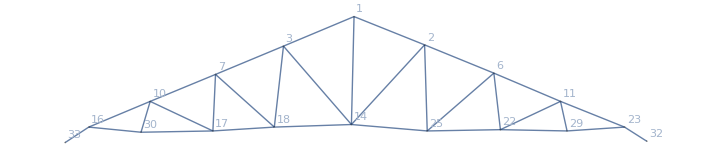

```mathematica
actualGraph
vertexList=actualGraph//VertexList;
vertexCoordinate= PropertyValue[actualGraph,VertexCoordinates];
appliedForces= {{3,{FS1,3*Pi/2}},{1,{FS2,3*Pi/2}},{2,{FS3,3*Pi/2}}};(*Force={Vertex, Force, Angle}*)
supportForces={{16,{S1,Pi/2}},{23,{S2,Pi/2}}};(*Support Forces={Perpendicular to the support base queue,Parallel to the base support queue}*)
parallelSuppor={{16,{Sp,0}}};(*Parallel to the base support queue*)
```

```mathematica
solvingForces[actualGraph,vertexList,vertexCoordinate,appliedForces,supportForces,parallelSuppor]
```

{{F[2]→0.-0.966992 FS1-1.31744 FS2-0.954943 FS3,F[3]→-0.99288 FS1-1.32657 FS2-0.98051 FS3,F[14]→0.754129 FS1+0.0169059 FS2+0.744733 FS3,F[667]→0.764694 FS1+1.04183 FS2+1.31897 FS3,F[736]→0.,F[253]→-0.824027 FS1-1.12267 FS2-1.42131 FS3,F[319]→-0.0688345 FS1-0.0937813 FS2-0.118728 FS3,F[638]→0.777695 FS1+1.05954 FS2+1.34139 FS3,F[480]→1.21736 FS1+0.965491 FS2+0.713624 FS3,F[528]→0.,F[160]→-1.31643 FS1-1.04406 FS2-0.771699 FS3,F[300]→-0.149915 FS1-0.118898 FS2-0.0878814 FS3,F[510]→1.2535 FS1+0.994155 FS2+0.73481 FS3,F[28]→0.0947285 FS1+0.12906 FS2-0.821654 FS3,F[12]→-0.897924 FS1-1.22335 FS2-1.54877 FS3,F[50]→-0.0909378 FS1-0.123895 FS2-0.156852 FS3,F[42]→-0.921476 FS1+0.0337379 FS2+0.0249367 FS3,F[21]→-1.63482 FS1-1.29659 FS2-0.958346 FS3,F[54]→-0.0511343 FS1-0.0405548 FS2-0.0299753 FS3,F[252]→1.51214 FS1+1.19928 FS2+0.886424 FS3,F[350]→0.835114 FS1+1.13777 FS2+1.44043 FS3,F[150]→0.00672834 FS1+0.0091668 FS2+0.0116053 FS3,F[66]→-0.898585 FS1-1.22425 FS2-1.54991 FS3,F[132]→0.00727252 FS1+0.0099082 FS2+0.0125439 FS3,F[126]→0.132787 FS1+0.105313 FS2+0.0778404 FS3,F[70]→-1.51976 FS1-1.20533 FS2-0.890896 FS3,F[119]→-0.138064 FS1-0.109499 FS2-0.0809339 FS3,F[306]→1.41033 FS1+1.11854 FS2+0.826745 FS3,F[550]→0.824401 FS1+1.12318 FS2+1.42195 FS3,F[170]→0.164006 FS1+0.130074 FS2+0.0961414 FS3,F[242]→0.0527032 FS1+0.0718037 FS2+0.0909041 FS3,S1→0.636585 FS1+0.504878 FS2+0.373171 FS3,S2→0.363415 FS1+0.495122 FS2+0.626829 FS3,Sp→8.52651×10^-14 FS1+1.27898×10^-13 FS2+1.42109×10^-13 FS3}}

### 3

### 4

### 5